```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Thu 18 Jan 2018 23:45:26

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 11

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 5 Further Topics in Calculus

## Lab 34: Conic Sections and Parametric Equations

Introduction

Demonstration: Plane Cross Sections of the Surface of a Cone

Exercises:

a.

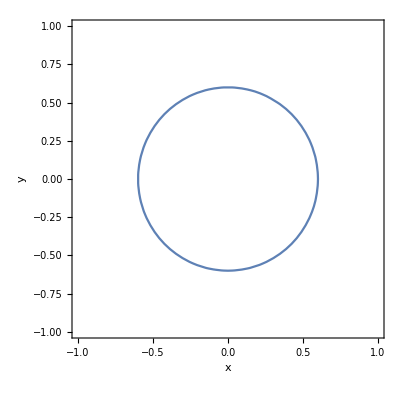

```mathematica
ContourPlot[x^2+y^2==0.6^2,{x,-1,1},{y,-1,1},FrameLabel->Automatic]
```

The equation of a unit circle is x^2+y^2==1.

b.

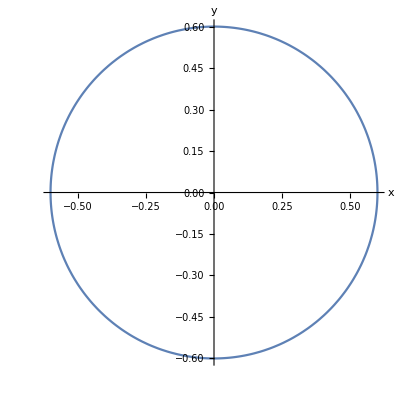

```mathematica
ParametricPlot[0.6{Cos[θ],Sin[θ]},{θ,0,2π},AxesLabel->{x,y}]
```

c.

d.

The standard form of an ellipse is x^2/a^2+y^2/b^2==1.

e.

```mathematica
x^2/a^2+y^2/b^2==1
SCMAF[%,RA,{All,{x==a Cos[θ],y==b Sin[θ]}},Apply->Simplify]
```

x^2/a^2+y^2/b^2==1

True

f.

```mathematica
√((x+f)^2+y^2)+√((x-f)^2+y^2)==c
SCMAF[%,RA,{All,c==2a},
SCMoveTerm,{All,√((x-f)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCEqMove,{All,4a √((-f+x)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCMoveTerm,{All,At[2]},
SCEliminate,{All,x^2/a^2+y^2/b^2==1,y^2},
Collect,{All,x}]
```

√((-f+x)^2+y^2)+√((f+x)^2+y^2)==c

-16 a^4+16 a^2 f^2+16 a^2 x^2-16 f^2 x^2+16 b^2 (a^2-x^2)==0

-16 a^4+16 a^2 b^2+16 a^2 f^2+(16 a^2-16 b^2-16 f^2) x^2==0

To satisfy this equation for any x,

```mathematica
SCSolve[16 a^2-16 b^2-16 f^2==0,f]
```

{{f==-√(a^2-b^2)},{f==√(a^2-b^2)}}

```mathematica
SCSolve[-16 a^4+16 a^2 b^2+16 a^2 f^2==0,f]
```

{{f==-√(a^2-b^2)},{f==√(a^2-b^2)}}

g.

The standard form of a hyperbola is x^2/a^2-y^2/b^2==1.

h.

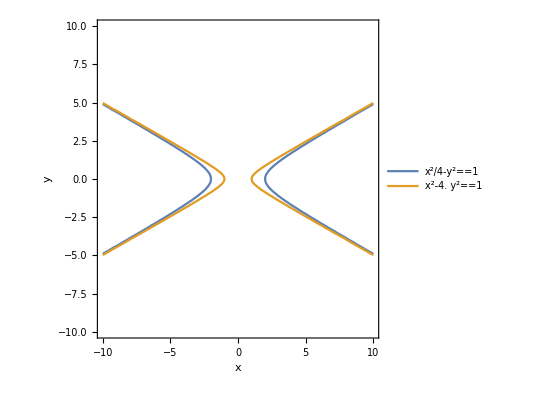

```mathematica
ContourPlot[Evaluate@{(x^2/a^2-y^2/b^2==1/.{a->2,b->1}),(x^2/a^2-y^2/b^2==1/.{a->1,b->0.5})},{x,-10,10},{y,-10,10},PlotLegends->"Expressions",FrameLabel->Automatic]
```

i.

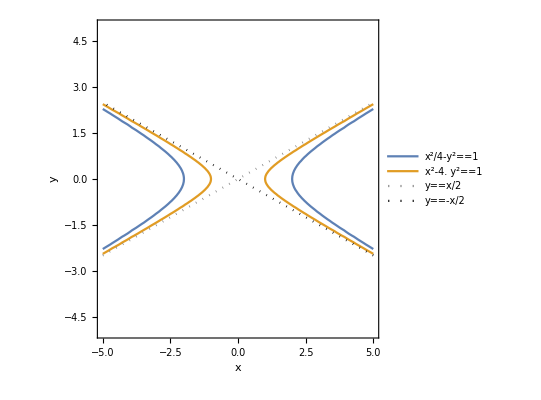

```mathematica
ContourPlot[Evaluate@{(x^2/a^2-y^2/b^2==1/.{a->2,b->1}),(x^2/a^2-y^2/b^2==1/.{a->1,b->0.5}),(y==b/a x/.{a->2,b->1}),(y==-b/a x/.{a->2,b->1})},{x,-5,5},{y,-5,5},ContourStyle->{Automatic,Automatic,{Gray,Dotted},{Black,Dotted}},PlotLegends->"Expressions",Axes->True,FrameLabel->Automatic]
```

j.

```mathematica
√((x+f)^2+y^2)-√((x-f)^2+y^2)==c
SCMAF[%,RA,{All,c==2a},
SCMoveTerm,{All,√((x-f)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,
SCEqMove,{All,4a √((-f+x)^2+y^2)},
#^2&,All,Level->{1},Apply->Expand,,
SCMoveTerm,{All,At[2]},
SCEliminate,{All,x^2/a^2-y^2/b^2==1,y^2},
Collect,{All,x}]
```

-√((-f+x)^2+y^2)+√((f+x)^2+y^2)==c

16 a^2 f^2-32 a^2 f x+16 a^2 x^2+16 a^2 y^2==16 a^4-32 a^2 f x+16 f^2 x^2

-16 a^4+16 a^2 f^2+16 a^2 x^2-16 f^2 x^2-16 b^2 (a^2-x^2)==0

-16 a^4-16 a^2 b^2+16 a^2 f^2+(16 a^2+16 b^2-16 f^2) x^2==0

To satisfy this equation for any x,

```mathematica
SCSolve[16 a^2+16 b^2-16 f^2==0,f]
```

{{f==-√(a^2+b^2)},{f==√(a^2+b^2)}}

```mathematica
SCSolve[-16 a^4-16 a^2 b^2+16 a^2 f^2==0,f]
```

{{f==-√(a^2+b^2)},{f==√(a^2+b^2)}}

k.

l.

The standard equation for a hyperboloid is x^2/a^2+y^2/b^2-z^2/c^2==1.

```mathematica
ContourPlot3D[Evaluate[x^2/a^2+y^2/b^2-z^2/c^2==1/.{a->1,b->1,c->1}],{x,-5,5},{y,-5,5},{z,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
x^2/a^2+y^2/b^2-z^2/c^2==1
SCMAF[%,RA,{All,{a==1,b==1,c==1}},
RA,{At[1],{x==Cos[u]+ v Sin[u],y== Sin[u]- v Cos[u]}},
SCSolve,{All,z,Rule->True},Apply->FullSimplify]
```

x^2/a^2+y^2/b^2-z^2/c^2==1

-z^2+(-v Cos[u]+Sin[u])^2+(Cos[u]+v Sin[u])^2==1

{{z→-√(v^2)},{z→√(v^2)}}

```mathematica
ParametricPlot3D[{Cos[u]+v Sin[u],Sin[u]-v Cos[u],v},{u,0,2π},{v,-10,10},AxesLabel->{x,y,z}]
```

-Graphics3D-

m.

The standard equation for an ellipsoid is x^2/a^2+y^2/b^2+z^2/c^2==1.

```mathematica
ContourPlot3D[Evaluate[x^2/a^2+y^2/b^2+z^2/c^2==1/.{a->3,b->2,c->1}],{x,-3,3},{y,-3,3},{z,-3,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
x^2/a^2+y^2/b^2+z^2/c^2==1
SCMAF[%,RA,{At[1],{x==a Cos[u]Sin[v],y==b Sin[u]Sin[v],z==c Cos[v]}},Apply->FullSimplify]
```

x^2/a^2+y^2/b^2+z^2/c^2==1

True

```mathematica
ParametricPlot3D[Evaluate[{a Cos[u]Sin[v],b Sin[u]Sin[v],c Cos[v]}/.{a->3,b->2,c->1}],{u,0,2π},{v,0,2π},PlotRange->{{-3,3},{-3,3},{-3,3}},AxesLabel->{x,y,z}]
```

-Graphics3D-

## Lab 35: Hyperbolic Functions

Introduction

```mathematica
x^2+y^2==1
SCMAF[%,RA,{At[1],{x==Cos[θ],y==Sin[θ]}},Apply->Simplify]
```

x^2+y^2==1

True

```mathematica
x^2-y^2==1
SCMAF[%,RA,{At[1],{x==Cosh[θ],y==Sinh[θ]}},Apply->Simplify]
```

x^2-y^2==1

True

Defining cosh(μ) and sinh(μ).

Exercises:

a, b.

```mathematica
x^2-y^2==1
SCMAF[%,SCSolve,{All,y}]
```

x^2-y^2==1

{{y==-√(-1+x^2)},{y==√(-1+x^2)}}

```mathematica
SCAFE[∫_1^x √(-1+s^2)ⅆs,SCEvalInt]
SCMAF[%,Refine,{All,x≥1},
SCEliminate,{At[2],y==√(-1+x^2),√(-1+x^2)}]
```

ConditionalExpression[∫_1^x √(-1+s^2)ⅆs==1/2 (x √(-1+x^2)-Log[x+√(-1+x^2)]),x≥1]

∫_1^x √(-1+s^2)ⅆs==1/2 (x √(-1+x^2)-Log[x+√(-1+x^2)])

∫_1^x √(-1+s^2)ⅆs==1/2 (x y-Log[x+y])

c.

```mathematica
S==2((x y)/2-∫_1^x √(-1+s^2)ⅆs)
SCMAF[%,RR,{At[2],{∫_1^x_ √(-1+s^2)ⅆs==1/2 (x y-Log[x+y]),x==Cosh[μ],y==Sinh[μ]}},
FullSimplify,{At[2],Assumptions->μ>0}]
```

S==2 ((x y)/2-∫_1^x √(-1+s^2)ⅆs)

S==2 (1/2 Cosh[μ] Sinh[μ]+1/2 (Log[Cosh[μ]+Sinh[μ]]-Cosh[μ] Sinh[μ]))

S==μ

d.

```mathematica
S==2((x y)/2-∫_1^x √(-1+s^2)ⅆs)
SCMAF[%,RA,{All,{S==μ,∫_1^x_ √(-1+s^2)ⅆs==1/2 (x y-Log[x+y])}},
FullSimplify,{At[2],Assumptions->μ>0},
ⅇ^#&,All,Level->{1}]
```

S==2 ((x y)/2-∫_1^x √(-1+s^2)ⅆs)

μ==Log[x+y]

ⅇ^μ==x+y

e.

```mathematica
SCAFE[∫_1^x -√(-1+s^2)ⅆs,SCEvalInt]
SCMAF[%,Refine,{All,x≥1},
SCEliminate,{At[2],y==-√(-1+x^2),√(-1+x^2)},
SCMultEq,{All,-1}]
```

ConditionalExpression[∫_1^x -√(-1+s^2)ⅆs==1/2 (-x √(-1+x^2)+Log[x+√(-1+x^2)]),x≥1]

-∫_1^x √(-1+s^2)ⅆs==1/2 (x y+Log[x-y])

∫_1^x √(-1+s^2)ⅆs==1/2 (-x y-Log[x-y])

```mathematica
-S/2==(x y)/2-∫_1^x -√(-1+s^2)ⅆs
SCMAF[%,SCFactorInt,At[2],
RR,{All,{S==-μ,∫_1^x_ √(-1+s^2)ⅆs==1/2 (-x y-Log[x-y])}},
SCMultEq,{All,-2},Apply->ExpandAll,
ⅇ^#&,All,Level->{1}]
```

-S/2==(x y)/2-∫_1^x -√(-1+s^2)ⅆs

-μ==Log[x-y]

ⅇ^-μ==x-y

```mathematica
{ⅇ^μ==x+y,ⅇ^-μ==x-y}
SCMAF[%,RA,{All,{x==Cosh[μ],y==Sinh[μ]}},
SCSolve,{All,{Cosh[μ],Sinh[μ]}},Apply->Expand,
SCFactor,{{ⅇ^-μ/2+ⅇ^μ/2,1/2},{-ⅇ^-μ/2+ⅇ^μ/2,1/2}}]
```

{ⅇ^μ==x+y,ⅇ^-μ==x-y}

{Cosh[μ]==ⅇ^-μ/2+ⅇ^μ/2,Sinh[μ]==-ⅇ^-μ/2+ⅇ^μ/2}

{Cosh[μ]==1/2 (ⅇ^-μ+ⅇ^μ),Sinh[μ]==1/2 (-ⅇ^-μ+ⅇ^μ)}

Properties of cosh(μ) and sinh(μ).

f.

```mathematica
{cosh[μ]==(ⅇ^μ+ⅇ^-μ)/2,sinh[μ]==(ⅇ^μ-ⅇ^-μ)/2}
SCMAF[%,RA,{All,μ==1},Apply->N]
```

{cosh[μ]==1/2 (ⅇ^-μ+ⅇ^μ),sinh[μ]==1/2 (-ⅇ^-μ+ⅇ^μ)}

{cosh[1.]==1.54308,sinh[1.]==1.1752}

```mathematica
{cosh[μ]==Cosh[μ],sinh[μ]==Sinh[μ]}/.μ->1//N
```

{cosh[1.]==1.54308,sinh[1.]==1.1752}

g.

```mathematica
{tanh[x]==sinh[x]/cosh[x],tanh[x]==sinh[x]/cosh[x]}
SCMAF[%,RA,{All,{cosh[μ_]==(ⅇ^μ+ⅇ^-μ)/2,sinh[μ_]==(ⅇ^μ-ⅇ^-μ)/2}}]
```

{tanh[x]==sinh[x]/cosh[x],tanh[x]==sinh[x]/cosh[x]}

{tanh[x]==(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x),tanh[x]==(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x)}

h.

```mathematica
SCAFE[ⅆCosh[x]/ⅆx,TrigToExp,Cosh[x],ApplyAll->SCEvalDeriv]
SCMAF[%,SCExpToTrig,At[2]]
```

ⅆCosh[x]/ⅆx==-ⅇ^-x/2+ⅇ^x/2

ⅆCosh[x]/ⅆx==Sinh[x]

```mathematica
SCAFE[ⅆSinh[x]/ⅆx,TrigToExp,Sinh[x],ApplyAll->SCEvalDeriv]
SCMAF[%,SCExpToTrig,At[2]]
```

ⅆSinh[x]/ⅆx==ⅇ^-x/2+ⅇ^x/2

ⅆSinh[x]/ⅆx==Cosh[x]

```mathematica
SCAFE[{ⅆCosh[x]/ⅆx,ⅆSinh[x]/ⅆx},SCEvalDeriv]//Thread
```

{ⅆCosh[x]/ⅆx==Sinh[x],ⅆSinh[x]/ⅆx==Cosh[x]}

i.

```mathematica
SCARA[Underscript[Limit, x->∞][Sech[x]],Sech[x]==2/(ⅇ^x+ⅇ^-x),Apply->SCEvalLimit]
```

Limit_(x→∞)[Sech[x]]==0

```mathematica
SCARA[Underscript[Limit, x->∞][Csch[x]],Csch[x]==2/(ⅇ^x-ⅇ^-x),Apply->SCEvalLimit]
```

Limit_(x→∞)[Csch[x]]==0

```mathematica
SCAFE[{Underscript[Limit, x->∞][Sech[x]],Underscript[Limit, x->∞][Csch[x]]},SCEvalLimit]//Thread
```

{Limit_(x→∞)[Sech[x]]==0,Limit_(x→∞)[Csch[x]]==0}

## Lab 36: Sequences

Introduction

Exercises:

a.

```mathematica
Subscript[f, n]==5 4^n;
```

b.

c.

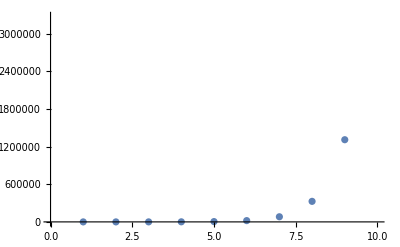

```mathematica
ListPlot@Table[5 4^n,{n,10}]
```

d.

e.

```mathematica
SCAFE[Underscript[Limit, n->∞][a b^n],SCEvalLimit]
```

ConditionalExpression[Limit_(n→∞)[a b^n]==∞,a>0&&Log[b]>0]

f.

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->5 4^n},
Reduce,{All,n,Reals}]
```

f_(1+n)>f_n

5 4^(1+n)>5 4^n

True

g.

```mathematica
SCAFE[Underscript[Limit, n->∞][(-1)^n/n],SCEvalLimit]
```

Limit_(n→∞)[(-1)^n/n]==0

h.

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->(-1)^n/n},
Reduce,{All,n,Reals}]
```

f_(1+n)>f_n

(-1)^(1+n)/(1+n)>(-1)^n/n

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

SCMAF::stopped: Stopped due to error.

Reduce[(-1)^(1+n)/(1+n)>(-1)^n/n,n,ℝ]

```mathematica
Subscript[f, n+1]>Subscript[f, n]
SCMAF[%,RA,{All,Subscript[f, n_]->(-1)^n/n},
Simplify,{All,Assumptions->{n>0,n∈Integers}}]
```

f_(1+n)>f_n

(-1)^(1+n)/(1+n)>(-1)^n/n

(-1)^(1+n)>0

i.

```mathematica
Subscript[s, k]==∑_(n=1)^k Subscript[f, n]
SCMAF[%,RA,{At[2],Subscript[f, n_]->n},Apply->SCEvalSum]
```

s_k==∑_(n=1)^k f_n

s_k==1/2 k (1+k)

j.

```mathematica
Subscript[s, k]==∑_(n=1)^k Subscript[f, n]
SCMAF[%,RA,{At[2],Subscript[f, n_]->(1/2)^n},Apply->SCEvalSum]
```

s_k==∑_(n=1)^k f_n

s_k==2^-k (-1+2^k)

k, l.

s_k==2^-k (-1+2^k)

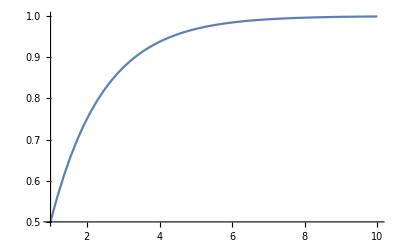

```mathematica
Subscript[s, k]==2^-k (-1+2^k)
SCMAF[%,Plot,{At[2],{k,1,10}},Part->2]
```

m.

```mathematica
SCARA[Underscript[Limit, k->∞][Subscript[s, k]],Subscript[s, k]==2^-k (-1+2^k),Apply->SCEvalLimit]
```

Limit_(k→∞)[s_k]==1

## Lab 37: An Introduction to Series

Geometric series

a.

```mathematica
Subscript[S, k]==∑_(n=1)^k 12/5^(n-1)
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k 12 5^(1-n)

S_k==3 5^(1-k) (-1+5^k)

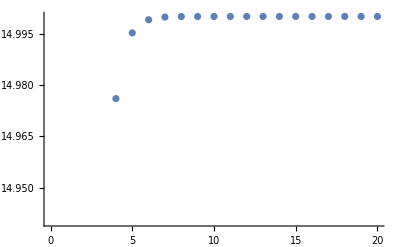

```mathematica
ListPlot@Table[3 5^(1-k) (-1+5^k),{k,20}]
```

b.

```mathematica
SCAFE[Underscript[Limit, k->∞][∑_(n=1)^k 12/5^(n-1)],SCEvalSum,Apply->SCEvalLimit]
```

Limit_(k→∞)[∑_(n=1)^k 12 5^(1-n)]==15

```mathematica
SCAFE[∑_(n=1)^∞ 12/5^(n-1),SCEvalSum,Apply->ExpandAll]
```

∑_(n=1)^∞ 12 5^(1-n)==15

d.

```mathematica
SCAFE[∑_(n=1)^∞ 12/5^n,SCFactor,{5^-n,1/5,Times->True}]
```

∑_(n=1)^∞ 12 5^-n==12/5 ∑_(n=1)^∞ 1·5^(1-n)

e.

```mathematica
Subscript[S, k]==∑_(n=1)^k 12/5^n
SCMAF[%,SCEvalSum,At[2],Apply->ExpandAll]
```

S_k==∑_(n=1)^k 12 5^-n

S_k==3-3 5^-k

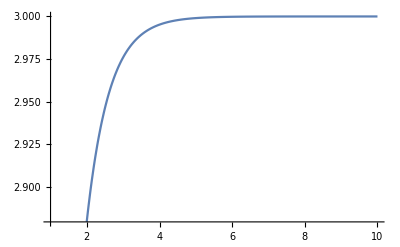

```mathematica
Plot[3-3 5^-k,{k,1,10}]
```

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ 12/5^n
SCMAF[%,SCEvalSum,At[2]]
```

S_∞==∑_(n=1)^∞ 12 5^-n

S_∞==3

f.

```mathematica
Subscript[S, k]==∑_(n=1)^k (12/5)^n
SCMAF[%,SCEvalSum,At[2],Apply->ExpandAll,
FullSimplify,At[2]]
```

S_k==∑_(n=1)^k (12/5)^n

S_k==-12/7+1/7 5^-k 12^(1+k)

S_k==12/7 (-1+(12/5)^k)

Keep in mind the convergence of geometric series.

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ a r^(n-1)
SCMAF[%,SCEvalSum,At[2]]
```

S_∞==∑_(n=1)^∞ a r^(-1+n)

S_∞==-a/(-1+r)

```mathematica
Subscript[S, ∞]==∑_(n=1)^∞ a r^(n-1)
SCMAF[%,SCEvalSum,{At[2],Assumptions->{Abs[r]≥1}}]
```

S_∞==∑_(n=1)^∞ a r^(-1+n)

Sum::div: Sum does not converge.

SCMAF::stopped: Stopped due to error.

S_∞==∑_(n=1)^∞ a r^(-1+n)

P-series

```mathematica
Subscript[S, k]==∑_(n=1)^k 1/n
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k 1/n

S_k==HarmonicNumber[k]

S_k==HarmonicNumber[k]

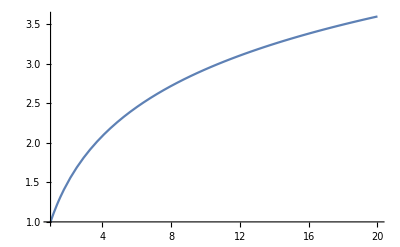

```mathematica
Subscript[S, k]==HarmonicNumber[k]
SCMAF[%,Plot,{At[2],{k,1,20}},Part->2]
```

```mathematica
Subscript[S, k]==∑_(n=1)^k 1/n^p
SCMAF[%,SCEvalSum,At[2]]
```

S_k==∑_(n=1)^k n^-p

S_k==HarmonicNumber[k,p]

{S_k,S_k,S_k,S_k}=={HarmonicNumber[k,1/3],HarmonicNumber[k,1/2],HarmonicNumber[k,4/3],HarmonicNumber[k,3/2]}

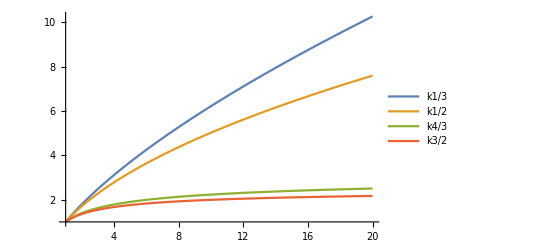

```mathematica
Table[Subscript[S, k]==HarmonicNumber[k,p],{p,{1/3,1/2,1+1/3,1+1/2}}]//Thread[#,Equal]&
SCMAF[%,Plot,{At[2],{k,1,20},PlotLegends->"Expressions"},Part->2]
```

## Lab 38: Convergence Tests for Series

Integral test
Given N∈ℤ, where f(n) is non-negative and monotonically decreasing on [N,∞),
∑_(n=N)^∞ f(n) converges if and only if ∫_N^∞ f(x)ⅆx converges.

a, b, c.

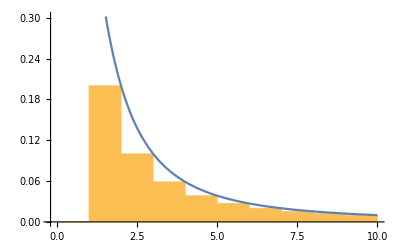

```mathematica
Show[RectangleChart[Prepend[Table[{1,1/(n^2+1)},{n,2,10}],{1,0}],BarSpacing->None],Plot[1/(x^2+1),{x,1,10}]]
```

d.

```mathematica
SCAFE[∑_(n=1)^k 1/(n^2+1),SCEvalSum,All,Apply->FullSimplify]
```

∑_(n=1)^k 1/(1+n^2)==1/2 (-1+π Coth[π]-ⅈ HarmonicNumber[-ⅈ+k]+ⅈ HarmonicNumber[ⅈ+k])

```mathematica
SCAFE[∫_1^k 1/(x^2+1)ⅆx,SCEvalInt,{All,Assumptions->k>1}]
```

∫_1^k 1/(1+x^2)ⅆx==-π/4+ArcTan[k]

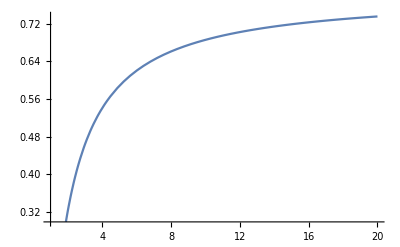

```mathematica
Plot[-π/4+ArcTan[k],{k,1,20}]
```

```mathematica
SCAFE[∫_1^∞ 1/(x^2+1)ⅆx,SCEvalInt]
```

∫_1^∞ 1/(1+x^2)ⅆx==π/4

e.

f.

Comparison test
If ∑_(n=N)^∞ a_n and ∑_(n=N)^∞ b_n are series with 0≤a_n≤b_n for all n≥N, then
1. if ∑_(n=N)^∞ a_n diverges, then ∑_(n=N)^∞ b_n diverges and
2. if ∑_(n=N)^∞ b_n converges, then ∑_(n=N)^∞ a_n converges.

a, b.

```mathematica
1/(n^2+1)≤1/n^p
SCMAF[%,RA,{All,p==2},
Reduce,{All,n}]
```

1/(1+n^2)≤n^-p

1/(1+n^2)≤1/n^2

n<0||n>0

```mathematica
SCAFE[∑_(n=1)^∞ 1/(n^2+1),SCEvalSum]
```

∑_(n=1)^∞ 1/(1+n^2)==1/2 (-1+π Coth[π])

c, d.

```mathematica
(6^(n-1)-1)/11^(n-1)≤a r^(n-1)
SCMAF[%,RA,{All,{a==1,r==6/11}},
Reduce,{All,n,Reals}]
```

11^(1-n) (-1+6^(-1+n))≤a r^(-1+n)

11^(1-n) (-1+6^(-1+n))≤(6/11)^(-1+n)

True

```mathematica
SCAFE[∑_(n=1)^∞ (6^(n-1)-1)/11^(n-1),SCEvalSum]
```

∑_(n=1)^∞ 11^(1-n) (-1+6^(-1+n))==11/10

e.

f, g.

```mathematica
ⅇ^n/n≥1/n^p
SCMAF[%,RA,{At[2],p==1},
Reduce,{All,n,Reals}]
```

ⅇ^n/n≥n^-p

ⅇ^n/n≥1/n

n≠0

Ratio test
Given the series ∑_(n=N)^∞ a_n and lim_(n→∞) |(a_(n+1))/a_n|=L, then
1. if L<1 then the series converges,
2. if L>1 then the series diverges,
3. if L=1 then the test is inconclusive.

a, b.

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[a, n+1]/Subscript[a, n]],Subscript[a, n_]->1/(n^2+1),Apply->SCEvalLimit]
```

Limit_(n→∞)[(a_(1+n))/a_n]==1

c, d.

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[a, n+1]/Subscript[a, n]],Subscript[a, n_]->e^n/(n!),Apply->SCEvalLimit]
```

Limit_(n→∞)[(a_(1+n))/a_n]==0

## Lab 39: Alternating Series

Demonstration: Sum of the Alternating Harmonic Series (I)

a, b, c, d.

```mathematica
SCAFE[Table[∑_(n=k)^(k+1) (-1)^(n-1)/n,{k,1,3,2}],SCEvalSum]
```

{∑_(n=1)^2 (-1)^(-1+n)/n,∑_(n=3)^4 (-1)^(-1+n)/n}=={1/2,1/12}

e.

```mathematica
SCAFE[∫_1^2 1/x ⅆx,SCEvalInt]
```

∫_1^2 1/x ⅆx==Log[2]

```mathematica
SCAFE[Underscript[Limit, k->∞][∑_(n=1)^k (-1)^(n-1)/n],SCEvalSum,Apply->SCEvalLimit]
```

Limit_(k→∞)[∑_(n=1)^k (-1)^(-1+n)/n]==Log[2]

Alternating series test
∑_(n=1)^∞ ((-1)^(n-1)a_n) converges if |a_(n+1)|<|a_n| for all n≥1 and lim_(n→∞) a_n=0.

f.

g.

h.

i.

```mathematica
Abs[(-3/5)^(n+1)]<Abs[(-3/5)^n]
SCMAF[%,Reduce,{All,n,Integers}]
```

|(-3/5)^(1+n)|<|(-3/5)^n|

n∈ℤ

j.

```mathematica
SCAFE[Underscript[Limit, n->∞][(3/5)^n],SCEvalLimit]
```

Limit_(n→∞)[(3/5)^n]==0

k.

l.

m.

## Lab 40: Taylor Series

a, b, c.

```mathematica
SCARA[∑_(n=0)^9 Subscript[Derivative[n][f][x], x==0]/(n!)x^n,f->Function[{x},Cos[x]],Apply->SCEvalSum]
SCMAF[%,SCEvalEqSub,At[2]]
```

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1/2 x^2 (-Cos[x])_(x==0)+1/720 x^6 (-Cos[x])_(x==0)+Cos[x]_(x==0)+1/24 x^4 Cos[x]_(x==0)+(x^8 Cos[x]_(x==0))/40320+x (-Sin[x])_(x==0)+1/120 x^5 (-Sin[x])_(x==0)+(x^9 (-Sin[x])_(x==0))/362880+1/6 x^3 Sin[x]_(x==0)+(x^7 Sin[x]_(x==0))/5040

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1-x^2/2+x^4/24-x^6/720+x^8/40320

```mathematica
∑_(n=0)^∞ Subscript[Derivative[n][f][x], x==0]/(n!)x^n==Series[Cos[x],{x,0,9}]
```

∑_(n=0)^∞ (x^n (f^(n)[x])_(x==0))/(n!)==1-x^2/2+x^4/24-x^6/720+x^8/40320+O[x]^10

```mathematica
SCAFE[Cos[x],SCPowerSeries,{All,n}]
```

Cos[x]==∑_(n=0)^∞ ((-1)^n x^(2 n))/((2 n)!)

d, e.

```mathematica
SCARA[∑_(n=0)^9 Subscript[Derivative[n][f][x], x==0]/(n!)x^n,f->Function[{x},ArcSin[x]],Apply->SCEvalSum]
SCMAF[%,SCEvalEqSub,At[2]]
```

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==1/2 x^2 (x/((1-x^2)^(3/2)))_(x==0)+x (1/(√(1-x^2)))_(x==0)+1/24 x^4 ((15 x^3)/((1-x^2)^(7/2))+(9 x)/((1-x^2)^(5/2)))_(x==0)+1/6 x^3 ((3 x^2)/((1-x^2)^(5/2))+1/((1-x^2)^(3/2)))_(x==0)+1/120 x^5 ((75 x^2)/((1-x^2)^(7/2))+9/((1-x^2)^(5/2))+3 x^2 ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2))))_(x==0)+1/720 x^6 ((420 x^3)/((1-x^2)^(9/2))+(180 x)/((1-x^2)^(7/2))+9 x ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2)))+3 x^2 ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))))_(x==0)+1/5040 x^7 ((2100 x^2)/((1-x^2)^(9/2))+180/((1-x^2)^(7/2))+60 x^2 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+9 ((35 x^2)/((1-x^2)^(9/2))+5/((1-x^2)^(7/2)))+15 x ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2))))+3 x^2 ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))))_(x==0)+1/40320 x^8 ((15120 x^3)/((1-x^2)^(11/2))+(5040 x)/((1-x^2)^(9/2))+180 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+60 x^2 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+24 ((70 x)/((1-x^2)^(9/2))+5 x ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2))))+21 x ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))))+3 x^2 ((1260 x)/((1-x^2)^(11/2))+70 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+10 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+5 x ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))))_(x==0)+1/362880 x^9 ((75600 x^2)/((1-x^2)^(11/2))+5040/((1-x^2)^(9/2))+1680 x^2 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+180 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+300 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+60 x^2 ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))+45 ((630 x^2)/((1-x^2)^(11/2))+70/((1-x^2)^(9/2))+5 ((63 x^2)/((1-x^2)^(11/2))+7/((1-x^2)^(9/2)))+5 x ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))))+27 x ((1260 x)/((1-x^2)^(11/2))+70 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+10 ((126 x)/((1-x^2)^(11/2))+7 x ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2))))+5 x ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))))+3 x^2 ((13860 x^2)/((1-x^2)^(13/2))+1260/((1-x^2)^(11/2))+70 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+70 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))+15 ((1386 x^2)/((1-x^2)^(13/2))+126/((1-x^2)^(11/2))+7 ((99 x^2)/((1-x^2)^(13/2))+9/((1-x^2)^(11/2)))+7 x ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))))+5 x ((2772 x)/((1-x^2)^(13/2))+126 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))+14 ((198 x)/((1-x^2)^(13/2))+9 x ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2))))+7 x ((2574 x^2)/((1-x^2)^(15/2))+198/((1-x^2)^(13/2))+9 ((143 x^2)/((1-x^2)^(15/2))+11/((1-x^2)^(13/2)))+9 x ((286 x)/((1-x^2)^(15/2))+11 x ((195 x^2)/((1-x^2)^(17/2))+13/((1-x^2)^(15/2))))))))_(x==0)+ArcSin[x]_(x==0)

∑_(n=0)^9 (x^n (f^(n)[x])_(x==0))/(n!)==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

```mathematica
∑_(n=0)^∞ Subscript[Derivative[n][f][x], x==0]/(n!)x^n==Series[ArcSin[x],{x,0,9}]
```

∑_(n=0)^∞ (x^n (f^(n)[x])_(x==0))/(n!)==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^10

```mathematica
SCAFE[ArcSin[x],SCPowerSeries,{All,n}]
```

ArcSin[x]==∑_(n=0)^∞ (4^-n x^(1+2 n) (2 n)!)/((1+2 n) (n!)^2)

f.

```mathematica
g[x]==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152
SCMAF[%,SCMultEq,{All,6},
RA,{All,x==1/2},Apply->N]
```

g[x]==x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152

6 g[x]==6 x+x^3+(9 x^5)/20+(15 x^7)/56+(35 x^9)/192

6. g[0.5]==3.14151

```mathematica
SCARA[6arcSin[1/2],{arcSin[x_]->∑_(n=0)^∞ (4^-n x^(1+2 n) (2 n)!)/((1+2 n) (n!)^2)},Apply->SCEvalSum]
```

6 arcSin[1/2]==π

## Project Set 5

### Project 1: Hex Numbers

a.


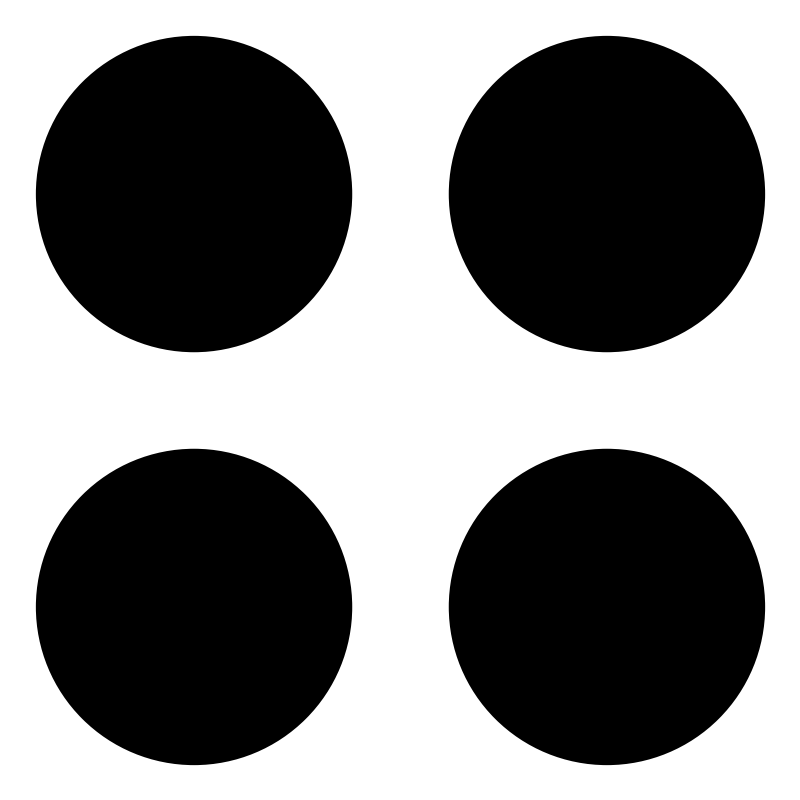
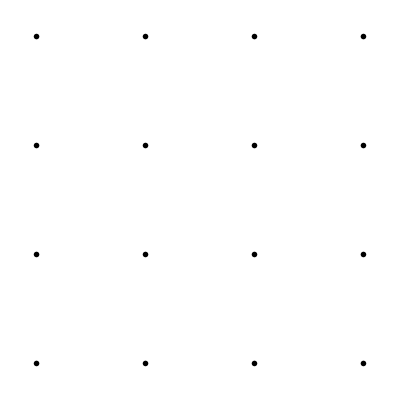
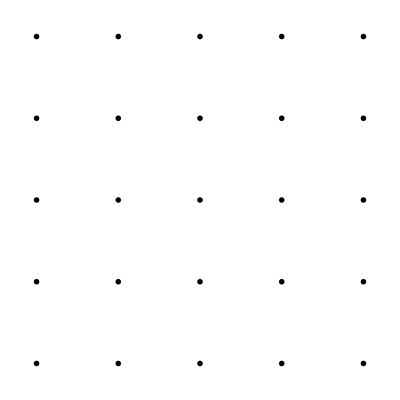
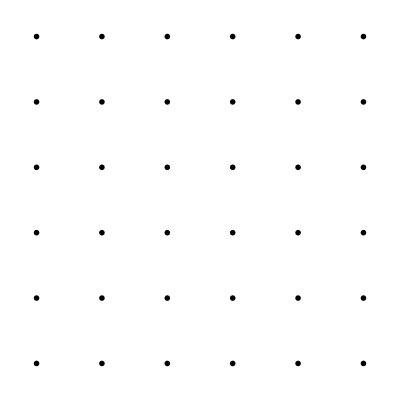
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphicsGrid@Table[Graphics@Disk[],{i,n},{j,n}],{n,6}]
```

```mathematica
Subscript[a, n]==n^2;
```

```mathematica
Subscript[a, n]==∑_(i=1)^n (2i-1)
SCMAF[%,SCEvalSum,At[2],Apply->Expand]
```

a_n==∑_(i=1)^n (-1+2 i)

a_n==n^2

```mathematica
Table[Subscript[a, n]==n^2,{n,6}]
```

{a_1==1,a_2==4,a_3==9,a_4==16,a_5==25,a_6==36}

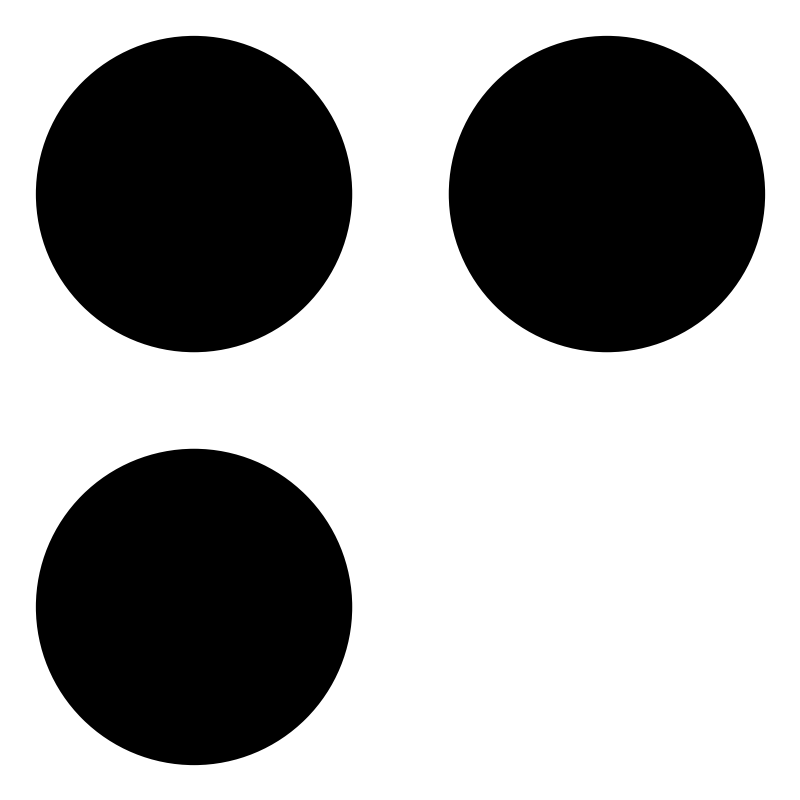
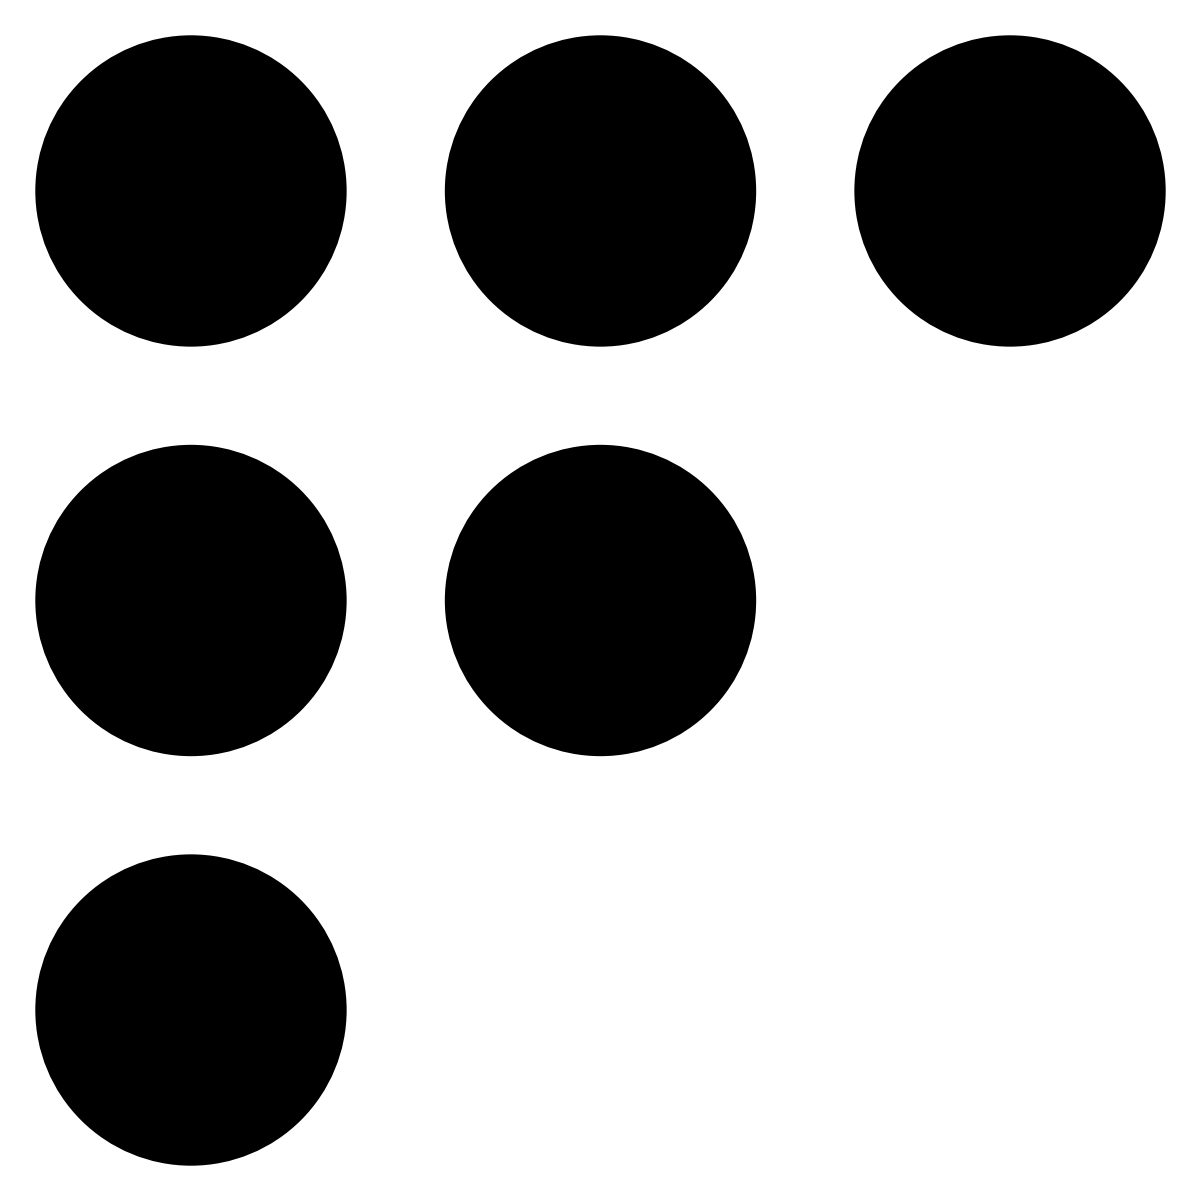
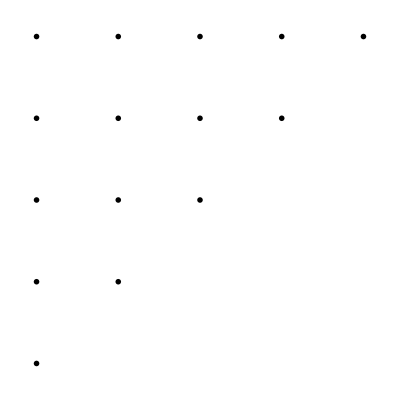
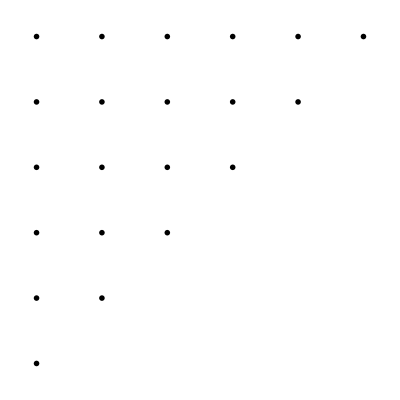
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphicsGrid@Reverse@Table[If[i≥j,Graphics@Disk[]],{i,n},{j,n}],{n,6}]
```

```mathematica
Subscript[b, n]==∑_(i=1)^n i
SCMAF[%,SCEvalSum,At[2]]
```

b_n==∑_(i=1)^n i

b_n==1/2 n (1+n)

```mathematica
Table[Subscript[b, n]==1/2 n (1+n),{n,6}]
```

{b_1==1,b_2==3,b_3==6,b_4==10,b_5==15,b_6==21}

b.

Discover pattern of one side.

```mathematica
Grid@{{{1/Tan[π/3],1}},
{{2/Tan[π/3],2},{2/Tan[π/3+π/3 1/2],2}},
{{3/Tan[π/3],3},{3/Tan[π/3+π/3 1/3],3},{3/Tan[π/3+π/3 2/3],3}},
{{4/Tan[π/3],4},{4/Tan[π/3+π/3 1/4],4},{4/Tan[π/3+π/3 2/4],4},{4/Tan[π/3+π/3 3/4],4}}}
```

{1/(√3),1} |  |  | 
{2/(√3),2} | {0,2} |  | 
{√3,3} | {3 Tan[π/18],3} | {-3 Tan[π/18],3} | 
{4/(√3),4} | {4/(2+√3),4} | {0,4} | {4/(-2-√3),4}

Then generate six sides using rotate of it.

```mathematica
Graphics@Table[Rotate[Point[{1,0}],π/3 n,{0,0}],{n,6}]
```

-Graphics-

The result is

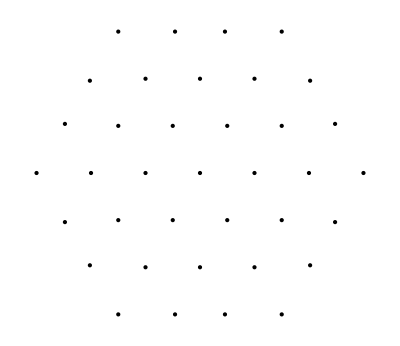

```mathematica
Graphics@Append[Table[Rotate[p,π/3 θ,{0,0}],{p,Point/@Table[{l/Tan[π/3+(n-1)/l π/3],l},{l,3},{n,l}]},{θ,6}],Point[{0,0}]]
```

Combine the points and edges of hexagons.

```mathematica
Show[Graphics@{PointSize[Large],Append[Table[Rotate[p,π/3 θ,{0,0}],{p,Point/@Table[{l/Tan[π/3+(n-1)/l π/3],l},{l,3},{n,l}]},{θ,6}],Point[{0,0}]]},
Graphics@Table[Style[RegularPolygon[l/Cos[π/6],6],EdgeForm[Black],Opacity[0]],{l,3}]]
```

-Graphics-

c.

```mathematica
Subscript[H, n]==FindSequenceFunction[{1,7,19,37,61,91},n]
```

H_n==1-3 n+3 n^2

d.

```mathematica
Subscript[S, k]==∑_(n=1)^k Subscript[H, n]
SCMAF[%,RA,{At[2],Subscript[H, n]==1-3 n+3 n^2},Apply->SCEvalSum]
```

S_k==∑_(n=1)^k H_n

S_k==k^3

e.

```mathematica
(x^2+4x+1)/(1-x)^3==Series[(x^2+4x+1)/(1-x)^3,{x,0,5}]
```

(1+4 x+x^2)/(1-x)^3==1+7 x+19 x^2+37 x^3+61 x^4+91 x^5+O[x]^6

f.

### Project 2: Limits Using Maclaurin Series

a.

```mathematica
SCAFE[x^2 ⅇ^x,SCPowerSeries,{All,n}]
SCMAF[%,SCSumChangeInterval,{At[2],{n,0,9}},Apply->SCEvalSum]
```

ⅇ^x x^2==x^2 ∑_(n=0)^∞ x^n/(n!)

ⅇ^x x^2==x^2 (1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880)

b.

```mathematica
SCAFE[Cos[x]-1,SCPowerSeries,{All,n}]
SCMAF[%,SCSumChangeInterval,{At[2],{n,0,9}},Apply->SCEvalSum]
```

-1+Cos[x]==-1+∑_(n=0)^∞ ((-1)^n x^(2 n))/((2 n)!)

-1+Cos[x]==-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000

c.

```mathematica
SCARR[(x^2 ⅇ^x)/(Cos[x]-1),{ⅇ^x x^2==x^2 (1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880),-1+Cos[x]==-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000}]
SCMAF[%,ExpandAll,At[2],Apply->FullSimplify]
```

(ⅇ^x x^2)/(-1+Cos[x])==(x^2 (1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880))/(-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200+x^16/20922789888000-x^18/6402373705728000)

(ⅇ^x x^2)/(-1+Cos[x])==-((17643225600 (362880+x (362880+x (181440+x (60480+x (15120+x (3024+x (504+x (72+x (9+x))))))))))/(3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16))

d.

```mathematica
SCARA[Underscript[Limit, x->0][(x^2 ⅇ^x)/(Cos[x]-1)],{(ⅇ^x x^2)/(-1+Cos[x])==-((17643225600 (362880+x (362880+x (181440+x (60480+x (15120+x (3024+x (504+x (72+x (9+x))))))))))/(3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16))},Apply->SCEvalLimit]
```

Limit_(x→0)[(ⅇ^x x^2)/(-1+Cos[x])]==-2

e.

```mathematica
SCAFE[Underscript[Limit, x->0][(Cos[x]-1)/x^2],SCEvalLimit]
```

Limit_(x→0)[(-1+Cos[x])/x^2]==-1/2

f.

```mathematica
SCAFE[Underscript[Limit, x->0][(x^2 ⅇ^x)/(Cos[x]-1)],SCEvalLimit]
```

Limit_(x→0)[(ⅇ^x x^2)/(-1+Cos[x])]==-2

### Project 3: A Focus on a Few Series of Interest

```mathematica
SCAFE[∑_(n=1)^∞ (n Cos[n]^2)/2^n,SCEvalSum,Apply->N]
```

∑_(n=1)^∞ 2^-n n Cos[n]^2==0.863098

a.

∑_(n=1)^∞ 2^-n n Cos[n]^2

{0.145963,0.232552,0.600084,0.706897,0.719469,0.8059,0.836983,0.837644,0.852237,0.859112,0.859112,0.861199,0.862505,0.862521,0.862785}

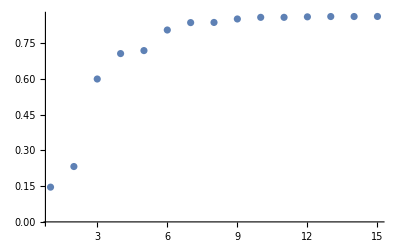

```mathematica
∑_(n=1)^∞ (n Cos[n]^2)/2^n
SCMAF[%,Table[SCSumChangeInterval[#,{n,1,k}],{k,1,15}]&,All,Apply->{N,SCEvalSum},
ListPlot,{All,PlotRange->All}]
```

b.

```mathematica
Subscript[a, n]≥0
SCMAF[%,RA,{At[1],Subscript[a, n]==(n Cos[n]^2)/2^n},
Reduce,{All,n,Integers}]
```

a_n≥0

2^-n n Cos[n]^2≥0

n∈ℤ&&n≥0

c.

```mathematica
Subscript[a, n]≤Subscript[b, n]
SCMAF[%,RA,{All,{Subscript[a, n]==(n Cos[n]^2)/2^n,Subscript[b, n]==n/2^n}}
,Reduce,{All,n,Integers}]
```

a_n≤b_n

2^-n n Cos[n]^2≤2^-n n

n==0||(n∈ℤ&&n≥1)

d.

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[b, n+1]/Subscript[b, n]],{Subscript[b, n_]->n/2^n},Apply->SCEvalLimit]
```

Limit_(n→∞)[(b_(1+n))/b_n]==1/2

Limit_(n→∞)[(b_(1+n))/b_n]<1, and by the ratio test, ∑_(n=1)^∞ b_n converges.

e.

0≤a_n≤b_n for all n≥1, and ∑_(n=1)^∞ b_n converges. Therefore, by the comparison test, ∑_(n=1)^∞ a_n converges.

Another series

```mathematica
SCAFE[∑_(n=1)^∞ (ⅇ^-n Cos[n]),SCEvalSum,Apply->{Chop,N}]
```

∑_(n=1)^∞ ⅇ^-n Cos[n]==0.0859726

```mathematica
SCAFE[∑_(n=1)^∞ (ⅇ^-n Cos[n]),SCEvalSum]
SCMAF[%,ComplexExpand,At[2],Apply->ExpandAll,
FullSimplify,At[2],Apply->N]
```

∑_(n=1)^∞ ⅇ^-n Cos[n]==-(-2 ⅇ^ⅈ+ⅇ+ⅇ^(1+2 ⅈ))/(2 (ⅇ^ⅈ-ⅇ) (-1+ⅇ^(1+ⅈ)))

∑_(n=1)^∞ ⅇ^-n Cos[n]==-(Cos[1]^2/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4))+(ⅇ Cos[1]^3)/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)+(ⅈ ⅇ^2 Cos[1] Sin[1])/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)-(ⅈ ⅇ Cos[1]^2 Sin[1])/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)+(ⅈ ⅇ^2 Cos[1] Cos[2] Sin[1])/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)-Sin[1]^2/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)+(ⅇ Cos[1] Sin[1]^2)/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)-(ⅈ ⅇ Sin[1]^3)/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)-ⅇ^2/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(3 ⅇ Cos[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ^3 Cos[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(3 ⅇ^2 Cos[1]^2)/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅇ^2 Cos[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ Cos[1] Cos[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ^3 Cos[1] Cos[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅇ^2 Cos[1]^2 Cos[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅈ ⅇ Sin[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅈ ⅇ^3 Sin[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅈ ⅇ Cos[2] Sin[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅈ ⅇ^3 Cos[2] Sin[1])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅇ^2 Sin[1]^2)/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ^2 Cos[2] Sin[1]^2)/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅇ^2 Cos[1] Sin[1] Sin[2])/(ⅇ^2-2 ⅇ Cos[1]-2 ⅇ^3 Cos[1]+Cos[1]^2+4 ⅇ^2 Cos[1]^2+ⅇ^4 Cos[1]^2-2 ⅇ Cos[1]^3-2 ⅇ^3 Cos[1]^3+ⅇ^2 Cos[1]^4+Sin[1]^2+ⅇ^4 Sin[1]^2-2 ⅇ Cos[1] Sin[1]^2-2 ⅇ^3 Cos[1] Sin[1]^2+2 ⅇ^2 Cos[1]^2 Sin[1]^2+ⅇ^2 Sin[1]^4)-(ⅈ ⅇ^2 Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅈ ⅇ Cos[1] Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅈ ⅇ^3 Cos[1] Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)-(ⅈ ⅇ^2 Cos[1]^2 Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ Sin[1] Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅇ^3 Sin[1] Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)+(ⅈ ⅇ^2 Sin[1]^2 Sin[2])/(2 ⅇ^2-4 ⅇ Cos[1]-4 ⅇ^3 Cos[1]+2 Cos[1]^2+8 ⅇ^2 Cos[1]^2+2 ⅇ^4 Cos[1]^2-4 ⅇ Cos[1]^3-4 ⅇ^3 Cos[1]^3+2 ⅇ^2 Cos[1]^4+2 Sin[1]^2+2 ⅇ^4 Sin[1]^2-4 ⅇ Cos[1] Sin[1]^2-4 ⅇ^3 Cos[1] Sin[1]^2+4 ⅇ^2 Cos[1]^2 Sin[1]^2+2 ⅇ^2 Sin[1]^4)

∑_(n=1)^∞ ⅇ^-n Cos[n]==0.0859726

f.

∑_(n=1)^∞ ⅇ^-n Cos[n]

{0.198766,0.142447,0.0931579,0.081186,0.0830973,0.0854774,0.0861648,0.086116,0.0860036,0.0859655,0.0859656,0.0859707,0.0859728,0.0859729,0.0859727}

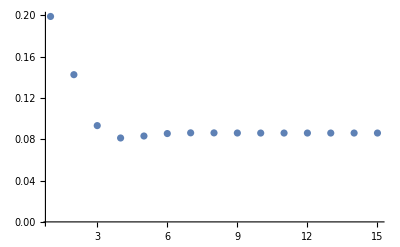

```mathematica
∑_(n=1)^∞ ⅇ^-n Cos[n]
SCMAF[%,Table[SCSumChangeInterval[#,{n,1,k}],{k,1,15}]&,All,Apply->{N,SCEvalSum},
ListPlot,{All,PlotRange->All}]
```

g.

```mathematica
Subscript[b, n]==ⅇ^-n Abs[Cos[n]];
```

h.

```mathematica
SCARA[∫_1^∞ Subscript[b, n] ⅆn,Subscript[b, n]==ⅇ^-n Abs[Cos[n]]]
SCMAF[%,SCEvalInt,At[2],
Simplify,At[2],Apply->N]
```

∫_1^∞ b_n ⅆn==∫_1^∞ ⅇ^-n |Cos[n]|ⅆn

∫_1^∞ b_n ⅆn==1/2 ⅇ^(-1-π/2) (ⅇ+ⅇ^(π/2) Cos[1]-ⅇ^(1+π/2) Cosh[π/2]+ⅇ^(1+π/2) Coth[π] Cosh[π/2]+ⅇ^(1+π/2) Csch[π] Cosh[π/2]-ⅇ^(π/2) Sin[1])

∫_1^∞ b_n ⅆn==0.161872

i.

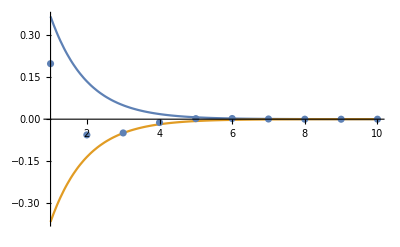

```mathematica
Show[Plot[{ⅇ^-n,-ⅇ^-n},{n,1,10},PlotRange->All],ListPlot@Table[ⅇ^-n Cos[n],{n,10}]]
```

```mathematica
SCARA[Underscript[Limit, n->∞][(Subscript[a, n])^(1/n)],Subscript[a, n]==ⅇ^-n Cos[n],Apply->SCEvalLimit]
```

Limit_(n→∞)[a_n^(1/n)]==Interval[{0,1/ⅇ}]

```mathematica
Underscript[Limit, n->∞][Subscript[a, n]^(1/n)]<1/.Underscript[Limit, n->∞][Subscript[a, n]^(1/n)]->Interval[{0,1/ⅇ}]
```

True

Therefore, by Cauchy root test, ∑_(n=1)^∞ a_n converges.

j.

```mathematica
SCAFE[∑_(n=1)^∞ (ⅇ^-n Sin[n]),SCEvalSum,Apply->{Chop,N}]
```

∑_(n=1)^∞ ⅇ^-n Sin[n]==0.41957

### Project 4: Derivatives Applied to Parametric Equations

a.

```mathematica
SCAFE[ⅆy/ⅆx,SCTransDeriv,{All,TransVar->{x,θ}}]
SCMAF[%,SCRecipDeriv,{ⅆθ/ⅆx},
RA,{At[2],{y==Sin[θ],x==Cos[θ]}},Apply->SCEvalDeriv,
TrigToExp,At[2],
SCEliminate,{At[2],TrigToExp@{y==Sin[θ],x==Cos[θ]},{ⅇ^(-ⅈ θ),ⅇ^(ⅈ θ)}}]
```

ⅆy/ⅆx==ⅆy/ⅆθ ⅆθ/ⅆx

ⅆy/ⅆx==(ⅈ (ⅇ^(-ⅈ θ)+ⅇ^(ⅈ θ)))/(ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ))

ⅆy/ⅆx==-x/y

b.

```mathematica
SCAFE[ⅆy/ⅆx,SCTransDeriv,{All,TransVar->{x,θ}}]
SCMAF[%,SCRecipDeriv,{ⅆθ/ⅆx},
RA,{At[2],{y==Tan[θ],x==Sec[θ]}},Apply->SCEvalDeriv,
TrigToExp,At[2],
SCEliminate,{At[2],TrigToExp@{y==Tan[θ],x==Sec[θ]},{ⅇ^(-ⅈ θ),ⅇ^(ⅈ θ)}},Apply->FullSimplify]
```

ⅆy/ⅆx==ⅆy/ⅆθ ⅆθ/ⅆx

ⅆy/ⅆx==-(2 ⅈ)/(ⅇ^(-ⅈ θ)-ⅇ^(ⅈ θ))

ⅆy/ⅆx==x/y

c.

```mathematica
y-Subscript[y, 1]==Subscript[(ⅆy/ⅆx), θ==π/4](x-Subscript[x, 1])
SCMAF[%,RR,{Subscript[(ⅆy/ⅆx), θ==π/4],{ⅆy/ⅆx==x/y,x==Sec[θ],y==Tan[θ]}},Apply->SCEvalEqSub,
RR,{All,{Subscript[x, 1]==Sec[θ],Subscript[y, 1]==Tan[θ],θ==π/4}}]
```

y-y_1==(x-x_1) (ⅆy/ⅆx)_(θ==π/4)

y-y_1==√2 (x-x_1)

-1+y==√2 (-√2+x)

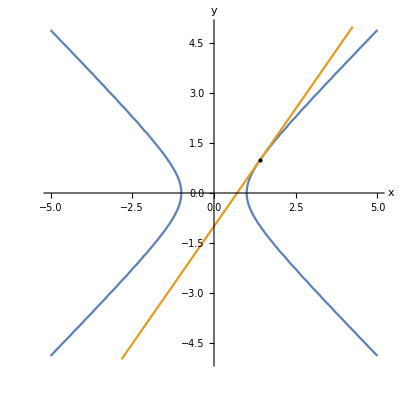

```mathematica
ContourPlot[{x^2-y^2==1,-1+y==√2 (-√2+x)},{x,-5,5},{y,-5,5},Epilog->Point[{Sec[π/4],Tan[π/4]}],Axes->True,Frame->False,AxesLabel->Automatic]
```

d.

```mathematica
SCAFE[∫_a^b √((ⅆy/ⅆx)^2+1)ⅆx,SCTransDeriv,{All,TransVar->{x,t}}]
SCMAF[%,SCFactor,{1+(ⅆt/ⅆx)^2 (ⅆy/ⅆt)^2,(ⅆt/ⅆx)^2},
PowerExpand,{At[2]},(* Assume ⅆt/ⅆx>0&&1/(ⅆt/ⅆx)^2+(ⅆy/ⅆt)^2>0 *)
SCTransInt,{At[2],TransVar->{x,t}},
SCRecipDeriv,{ⅆt/ⅆx}]
```

∫_a^b √(1+(ⅆy/ⅆx)^2)ⅆx==∫_a^b √(1+(ⅆt/ⅆx)^2 (ⅆy/ⅆt)^2)ⅆx

∫_a^b √(1+(ⅆy/ⅆx)^2)ⅆx==∫ⅆt/ⅆx ⅆx/ⅆt √(1/(ⅆt/ⅆx)^2+(ⅆy/ⅆt)^2)ⅆt

∫_a^b √(1+(ⅆy/ⅆx)^2)ⅆx==∫√((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt

```mathematica
SCARA[∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt,{a==0,b==2π,x==Cos[θ],y==Sin[θ],t==θ}]
SCMAF[%,SCEvalDeriv,At[2],Apply->SCEvalInt]
```

∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt==∫_0^(2 π) √((ⅆCos[θ]/ⅆθ)^2+(ⅆSin[θ]/ⅆθ)^2)ⅆθ

∫_a^b √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt==2 π

e.

```mathematica
SCAFE[∫_a^b 2π y √((ⅆy/ⅆx)^2+1)ⅆx,SCTransDeriv,{All,TransVar->{x,t}}]
SCMAF[%,SCFactor,{1+(ⅆt/ⅆx)^2 (ⅆy/ⅆt)^2,(ⅆt/ⅆx)^2},
PowerExpand,{At[2]},(* Assume ⅆt/ⅆx>0&&1/(ⅆt/ⅆx)^2+(ⅆy/ⅆt)^2>0 *)
SCTransInt,{At[2],TransVar->{x,t}},
SCRecipDeriv,{ⅆt/ⅆx}]
```

∫_a^b 2 π y √(1+(ⅆy/ⅆx)^2)ⅆx==2 π ∫_a^b y √(1+(ⅆt/ⅆx)^2 (ⅆy/ⅆt)^2)ⅆx

2 π ∫_a^b y √(1+(ⅆy/ⅆx)^2)ⅆx==2 π ∫y ⅆt/ⅆx ⅆx/ⅆt √(1/(ⅆt/ⅆx)^2+(ⅆy/ⅆt)^2)ⅆt

2 π ∫_a^b y √(1+(ⅆy/ⅆx)^2)ⅆx==2 π ∫y √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt

f.

```mathematica
SCARA[2 π ∫_0^π y √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt,{a==0,b==π,x==Cos[θ],y==
Sin[θ],t==θ}]
SCMAF[%,SCEvalDeriv,At[2],Apply->SCEvalInt]
```

2 π ∫_0^π y √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt==2 π ∫_0^π Sin[θ] √((ⅆCos[θ]/ⅆθ)^2+(ⅆSin[θ]/ⅆθ)^2)ⅆθ

2 π ∫_0^π y √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2)ⅆt==4 π

g.

```mathematica
SCAFE[∫_a^b π y^2 ⅆx,SCTransInt,{All,TransVar->{x,t}}]
```

∫_a^b π y^2ⅆx==π ∫y^2 ⅆx/ⅆtⅆt

```mathematica
SCARA[π ∫_a^b y^2 ⅆx/ⅆt ⅆt,{a==π,b==0,x==Cos[θ],y==
Sin[θ],t==θ}]
SCMAF[%,SCEvalDeriv,At[2],Apply->SCEvalInt]
```

π ∫_a^b y^2 ⅆx/ⅆtⅆt==π ∫_π^0 Sin[θ]^2 ⅆCos[θ]/ⅆθⅆθ

π ∫_a^b y^2 ⅆx/ⅆtⅆt==(4 π)/3

### Project 5: Radius of Convergence

a.

```mathematica
SCAFE[ⅇ^x,SCPowerSeries,{All,n}]
```

ⅇ^x==∑_(n=0)^∞ x^n/(n!)

```mathematica
SCARA[Underscript[Limit, n->∞][Abs[Subscript[a, n+1]/Subscript[a, n]]],Subscript[a, n_]->x^n/(n!),Apply->SCEvalLimit]
```

Limit_(n→∞)[|(a_(1+n))/a_n|]==0

b, f .

```mathematica
SCAFE[1/(1-x),SCPowerSeries,{All,n}]
```

1/(1-x)==∑_(n=0)^∞ x^n

```mathematica
Underscript[Limit, n->∞][Abs[Subscript[a, n+1]/Subscript[a, n]]]<1
SCMAF[%,RA,{At[1],Subscript[a, n_]->x^n},Apply->SCEvalLimit,
Reduce,{All,x,Reals}]
```

Limit_(n→∞)[|(a_(1+n))/a_n|]<1

|x|<1

-1<x<1

c.

```mathematica
SCAFE[4/(4+x),SCPowerSeries,{All,n}]
```

True

```mathematica
Series[4/(4+x),{x,0,4}]
```

1-x/4+x^2/16-x^3/64+x^4/256+O[x]^5

```mathematica
Underscript[Limit, n->∞][Abs[Subscript[a, n+1]/Subscript[a, n]]]<1
SCMAF[%,RA,{At[1],Subscript[a, n_]->((-1)^n x^n)/4^n},Apply->SCEvalLimit,
Reduce,{All,x,Reals}]
```

Limit_(n→∞)[|(a_(1+n))/a_n|]<1

(|x|)/4<1

-4<x<4

d, e.

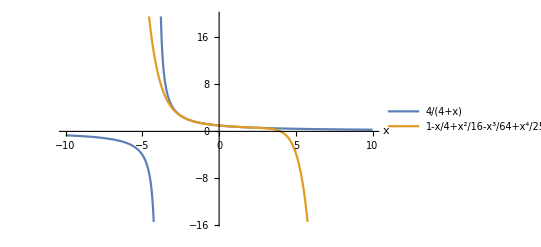

```mathematica
Plot[{4/(4+x),Evaluate@Normal@Series[4/(4+x),{x,0,9}]},{x,-10,10},AxesLabel->Automatic,PlotLegends->"Expressions"]
```

g.

```mathematica
Underscript[Limit, n->∞][Abs[Subscript[a, n+1]/Subscript[a, n]]]<1
SCMAF[%,RA,{At[1],Subscript[a, n_]->n! x^n},Apply->FullSimplify,
SCEvalLimit,At[1],
FullSimplify,{At[1],x∈Reals}]
```

Limit_(n→∞)[|(a_(1+n))/a_n|]<1

DirectedInfinity[|x|]<1

False

### Project 6: Fractal Sequence


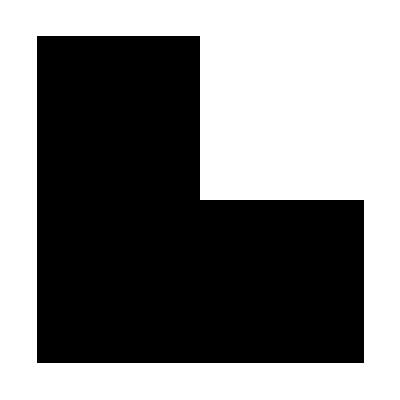
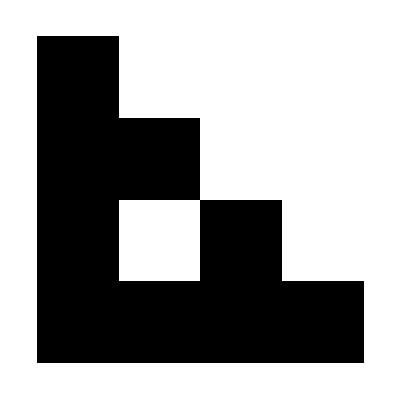
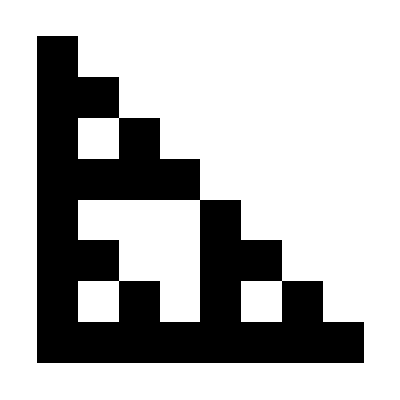
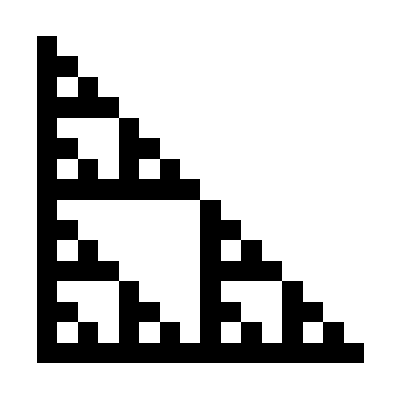
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},5]
```

From Mathematica Stack Exchange

```mathematica
CellularAutomaton[90,{{1},{0}},1020]//ArrayPlot
```

-Graphics-

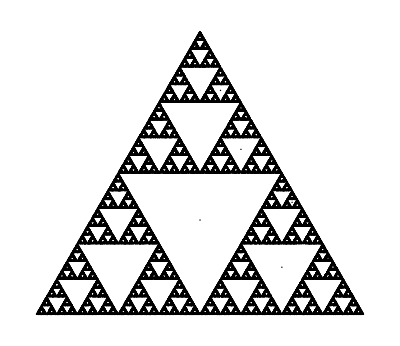

```mathematica
pts=N@CirclePoints[3];
Graphics[{AbsolutePointSize[1],Point@NestList[(#+RandomChoice[pts])/2&,{0,0},100000]}]
```

a.

```mathematica
{Subscript[a, 1]==(√3)/4,Subscript[p, 1]==3}
```

{a_1==(√3)/4,p_1==3}

```mathematica
{Subscript[a, 2]==Subscript[a, 1]-3^0/2 1/2^2(√3)/2,Subscript[p, 2]==Subscript[p, 1]+3^0 3/2}
SCMAF[%,RA,{All,{Subscript[a, 1]==(√3)/4,Subscript[p, 1]==3}}]
```

{a_2==-(√3)/16+a_1,p_2==3/2+p_1}

{a_2==(3 √3)/16,p_2==9/2}

b.

```mathematica
{Subscript[a, 3]==Subscript[a, 2]-3^1/2(1/2^2)^2(√3)/2,Subscript[p, 3]==Subscript[p, 2]+3^1 3/2^2}
SCMAF[%,RA,{All,{Subscript[a, 2]==(3 √3)/16,Subscript[p, 2]==9/2}}]
```

{a_3==-(3 √3)/64+a_2,p_3==9/4+p_2}

{a_3==(9 √3)/64,p_3==27/4}

c.

```mathematica
{Subscript[a, 4]==Subscript[a, 3]-3^2/2(1/2^3)^2(√3)/2,Subscript[p, 4]==Subscript[p, 3]+3^2 3/2^3}
SCMAF[%,RA,{All,{Subscript[a, 3]==(9 √3)/64,Subscript[p, 3]==27/4}}]
```

{a_4==-(9 √3)/256+a_3,p_4==27/8+p_3}

{a_4==(27 √3)/256,p_4==81/8}

d.

```mathematica
{Subscript[a, n]==Subscript[a, 1]+∑_(i=2)^n -3^(i-2)/2 1/4^(i-1)(√3)/2,Subscript[p, n]==Subscript[p, 1]+∑_(i=2)^n 3^(i-2)3/2^(i-1)}
SCMAF[%,SCEvalSum,All,
RA,{All,{Subscript[a, 1]==(√3)/4,Subscript[p, 1]==3}},
Simplify,All,Level->{2}]
```

{a_n==∑_(i=2)^n -3^(-3/2+i) 4^-i+a_1,p_n==∑_(i=2)^n (2/3)^(1-i)+p_1}

{a_n==(√3)/4+(4^(-1-n) (4 3^n-3 4^n))/(√3),p_n==3-2^-n (3 2^n-2 3^n)}

{a_n==3^(-1/2+n) 4^-n,p_n==2^(1-n) 3^n}

Using RSolve,

```mathematica
{Subscript[a, n+1]==Subscript[a, n]-3^(n-1)/2(1/2^n)^2(√3)/2,Subscript[p, n+1]==Subscript[p, n]+3^(n-1)3/2^n}
SCMAF[%,SCRSolve,{All,{Subscript[a, n],Subscript[p, n]},{n,1}},
RA,{All,{Subscript[a, 1]==(√3)/4,Subscript[p, 1]==3}},
Simplify,All,Level->{2}]
```

{a_(1+n)==-2^(-2-2 n) 3^(-1/2+n)+a_n,p_(1+n)==(3/2)^n+p_n}

{a_n==(√3)/4-1/3 2^(-2-2 n) (3 2^(2 n) √3-4 3^(1/2+n)),p_n==3+2^-n (-3 2^n+2 3^n)}

{a_n==3^(-1/2+n) 4^-n,p_n==2^(1-n) 3^n}

e.

```mathematica
Subscript[a, ∞]==Underscript[Limit, n->∞][Subscript[a, n]]
SCMAF[%,RA,{At[2],Subscript[a, n]==3^(-1/2+n) 4^-n},
SCEvalLimit,At[2]]
```

a_∞==Limit_(n→∞)[a_n]

a_∞==Limit_(n→∞)[3^(-1/2+n) 4^-n]

a_∞==0

```mathematica
Subscript[p, ∞]==Underscript[Limit, n->∞][Subscript[p, n]]
SCMAF[%,RA,{At[2],Subscript[p, n]==2^(1-n) 3^n},
SCEvalLimit,At[2]]
```

p_∞==Limit_(n→∞)[p_n]

p_∞==Limit_(n→∞)[2^(1-n) 3^n]

p_∞==∞

f.

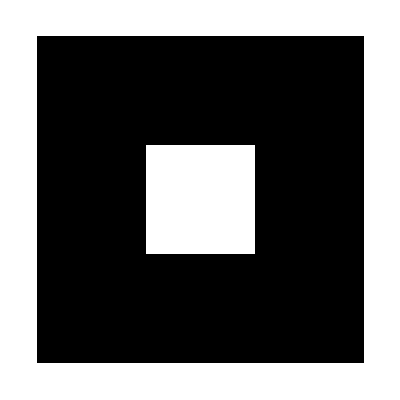
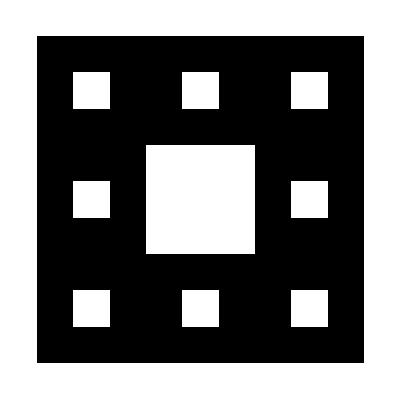
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]
```

List up a few terms,

```mathematica
{Subscript[a, 1]==1,Subscript[p, 1]==4};
```

```mathematica
{Subscript[a, 2]==Subscript[a, 1]-8^0(1/3)^2,Subscript[p, 2]==Subscript[p, 1]+8^0 4/3};
```

```mathematica
{Subscript[a, 3]==Subscript[a, 2]-8^1(1/3^2)^2,Subscript[p, 3]==Subscript[p, 2]+8^1 4/3^2};
```

```mathematica
{Subscript[a, 4]==Subscript[a, 3]-8^2(1/3^3)^2,Subscript[p, 4]==Subscript[p, 3]+8^2 4/3^3};
```

```mathematica
{Subscript[a, n+1]==Subscript[a, n]-8^(n-1)(1/3^n)^2,Subscript[p, n+1]==Subscript[p, n]+8^(n-1)4/3^n};
```

Manual formulation of the general term

```mathematica
{Subscript[a, n+1]==Subscript[a, 1]-∑_(i=2)^(n+1) 8^(i-2)(1/3^(i-1))^2,Subscript[p, n]==Subscript[p, 1]+∑_(i=2)^(n+1) 8^(i-2)4/3^(i-1)}
SCMAF[%,SCEvalSum,All,
RA,{All,{Subscript[a, 1]==1,Subscript[p, 1]==4}},
Simplify,{All},Level->{2}]
```

{a_(1+n)==-∑_(i=2)^(1+n) 3^(2-2 i) 8^(-2+i)+a_1,p_n==∑_(i=2)^(1+n) 2^(-4+3 i) 3^(1-i)+p_1}

{a_(1+n)==1-3^(-2 n) (3^(2 n)-8^n),p_n==4+4/5 3^-n (2^(3 n)-3^n)}

{a_(1+n)==(8/9)^n,p_n==4/5 3^-n (4 3^n+8^n)}

Find the general term using SCRSolve.

```mathematica
{Subscript[a, n+1]==Subscript[a, n]-8^(n-1)(1/3^n)^2,Subscript[p, n+1]==Subscript[p, n]+8^(n-1)4/3^n}
SCMAF[%,SCRSolve,{All,{Subscript[a, n],Subscript[p, n]},{n,1}},
RA,{All,{Subscript[a, 1]==1,Subscript[p, 1]==4}},
Simplify,All,Level->{2}]
```

{a_(1+n)==-3^(-2 n) 8^(-1+n)+a_n,p_(1+n)==2^(-1+3 n) 3^-n+p_n}

{a_n==1+8^(-1+n) 9^-n (9-8^(1-n) 9^n),p_n==4+1/10 3^-n (3 2^(3 n)-8 3^n)}

{a_n==(9/8)^(1-n),p_n==1/10 3^-n (32 3^n+3 8^n)}

```mathematica
Subscript[a, ∞]==Underscript[Limit, n->∞][Subscript[a, n]]
SCMAF[%,RA,{At[2],Subscript[a, n]==(9/8)^(1-n)},Apply->SCEvalLimit]
```

a_∞==Limit_(n→∞)[a_n]

a_∞==0

```mathematica
Subscript[p, ∞]==Underscript[Limit, n->∞][Subscript[p, n]]
SCMAF[%,RA,{At[2],Subscript[p, n]==1/10 3^-n (32 3^n+3 8^n)},Apply->SCEvalLimit]
```

p_∞==Limit_(n→∞)[p_n]

p_∞==∞

### Project 7: The Catenary

a.

y==a Cosh[x/a]

y==5 Cosh[x/5]

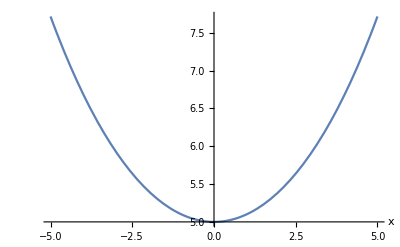

```mathematica
y==a Cosh[x/a]
SCMAF[%,RA,{At[2],a==5},
Plot,{At[2],{x,-5,5},AxesLabel->Automatic},Part->2]
```

b.

```mathematica
y==a Cosh[x/a]-b
SCMAF[%,RA,{All,{x==0,y==0,a==5}},
SCSolve,{All,b}]
```

y==-b+a Cosh[x/a]

0==5-b

b==5

c.

```mathematica
L==∫_Subscript[x, 1]^Subscript[x, 2] √(1+(ⅆy/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{y==a Cosh[x/a]-a,Subscript[x, 2]==r,Subscript[x, 1]->-r}},Apply->SCEvalDeriv,
SCEvalInt,{At[2],Assumptions->{a>0,r>0}},
RA,{At[1],L==100}]
```

L==∫_x_1^x_2 √(1+(ⅆy/ⅆx)^2)ⅆx

L==2 a Sinh[r/a]

100==2 a Sinh[r/a]

d.

```mathematica
y==a Cosh[x/a]-a
SCMAF[%,RA,{All,{y==25,x==r}}]
```

y==-a+a Cosh[x/a]

25==-a+a Cosh[r/a]

e.

```mathematica
{100==2 a Sinh[r/a],25==-a+a Cosh[r/a]}
SCMAF[%,SCSolve,{All,{r,a},Reals}]
```

{100==2 a Sinh[r/a],25==-a+a Cosh[r/a]}

{r==(75 Log[3])/2,a==75/2}

f.

y==-a+a Cosh[x/a]

y==-75/2+75/2 Cosh[(2 x)/75]

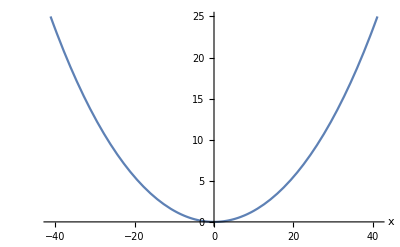

```mathematica
y==a Cosh[x/a]-a
SCMAF[%,RA,{At[2],{r==(75 Log[3])/2,a==75/2}},
Plot,{At[2],Evaluate[{x,-r,r}/.r->(75 Log[3])/2],AxesLabel->Automatic},Part->2]
```

g.

Let the lowest point of the catenary is located at y-axis.

```mathematica
SCARA[∫_0^Subscript[x, 2] √(1+(ⅆy/ⅆx)^2)ⅆx,y==a Cosh[x/a]-a,Apply->SCEvalDeriv]
SCMAF[%,SCEvalInt,{At[2],Assumptions->{a>0,Subscript[x, 2]>0}},
RA,{At[1],∫_0^Subscript[x, 2] √(1+(ⅆy/ⅆx)^2)ⅆx==Subscript[l, 2]}]
```

∫_0^x_2 √(1+(ⅆy/ⅆx)^2)ⅆx==∫_0^x_2 √(1+Sinh[x/a]^2)ⅆx

∫_0^x_2 √(1+(ⅆy/ⅆx)^2)ⅆx==a Sinh[x_2/a]

l_2==a Sinh[x_2/a]

By the same analogy, we can make the equation for l_1 and x_1.

```mathematica
{Subscript[l, 1]==a Sinh[Subscript[x, 1]/a],Subscript[l, 2]== a Sinh[Subscript[x, 2]/a],L==Subscript[l, 1]+Subscript[l, 2],Subscript[y, 1]==a Cosh[Subscript[x, 1]/a]-a,Subscript[y, 2]==a Cosh[Subscript[x, 2]/a]-a}
SCMAF[%,SCEliminate,{All,{Subscript[l, 1],Subscript[l, 2]}},
SCSolve,{All,{Subscript[x, 1],Subscript[x, 2],a,Reals}}]
```

{l_1==a Sinh[x_1/a],l_2==a Sinh[x_2/a],L==l_1+l_2,y_1==-a+a Cosh[x_1/a],y_2==-a+a Cosh[x_2/a]}

{L==a Sinh[x_1/a]+a Sinh[x_2/a],y_1==-a+a Cosh[x_1/a],y_2==-a+a Cosh[x_2/a]}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

SCMAF::stopped: Stopped due to error.

{False,False,False,False,False,False,False,False}

```mathematica
{Subscript[l, 1]==a Sinh[Subscript[x, 1]/a],Subscript[l, 2]== a Sinh[Subscript[x, 2]/a],L==Subscript[l, 1]+Subscript[l, 2],Subscript[y, 1]==a Cosh[Subscript[x, 1]/a]-a,Subscript[y, 2]==a Cosh[Subscript[x, 2]/a]-a}
SCMAF[%,Join,{All,{Cosh[Subscript[x, 1]/a]^2-Sinh[Subscript[x, 1]/a]^2==1,Cosh[Subscript[x, 2]/a]^2-Sinh[Subscript[x, 2]/a]^2==1}},
SCEliminate,{All,{Cosh[Subscript[x, 1]/a],Sinh[Subscript[x, 1]/a],Cosh[Subscript[x, 2]/a],Sinh[Subscript[x, 2]/a]},{1,2,4,5}},
SCSolve,{All,{a,Subscript[l, 1],Subscript[l, 2]}},
FullSimplify,All,Level->{3},Part->1(* Part 2 causes Subscript[l, 2]<0 for Subscript[y, 1]>Subscript[y, 2] *)]
```

{l_1==a Sinh[x_1/a],l_2==a Sinh[x_2/a],L==l_1+l_2,y_1==-a+a Cosh[x_1/a],y_2==-a+a Cosh[x_2/a]}

{{a==1/(2 (y_1-y_2)) (-L^2-y_1^2+(2 L^2 y_1)/(y_1-y_2)+y_2^2-(2 L √(y_1 y_2 (L^2-y_1^2+2 y_1 y_2-y_2^2)))/(y_1-y_2)),l_1==(L y_1-√(L^2 y_1 y_2-y_1^3 y_2+2 y_1^2 y_2^2-y_1 y_2^3))/(y_1-y_2),l_2==L-(L y_1)/(y_1-y_2)+(√(y_1 y_2 (L^2-y_1^2+2 y_1 y_2-y_2^2)))/(y_1-y_2)},{a==1/(2 (y_1-y_2)) (-L^2-y_1^2+(2 L^2 y_1)/(y_1-y_2)+y_2^2+(2 L √(y_1 y_2 (L^2-y_1^2+2 y_1 y_2-y_2^2)))/(y_1-y_2)),l_1==(L y_1+√(L^2 y_1 y_2-y_1^3 y_2+2 y_1^2 y_2^2-y_1 y_2^3))/(y_1-y_2),l_2==L-(L y_1)/(y_1-y_2)-(√(y_1 y_2 (L^2-y_1^2+2 y_1 y_2-y_2^2)))/(y_1-y_2)}}

{a==(-y_1^3+L^2 y_2+y_1^2 y_2-y_2^3-2 L √(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2))+y_1 (L^2+y_2^2))/(2 (y_1-y_2)^2),l_1==(L y_1-√(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2)))/(y_1-y_2),l_2==(-L y_2+√(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2)))/(y_1-y_2)}

```mathematica
{a==(-Subscript[y, 1]^3+L^2 Subscript[y, 2]+Subscript[y, 1]^2 Subscript[y, 2]-Subscript[y, 2]^3-2 L √(Subscript[y, 1] (L+Subscript[y, 1]-Subscript[y, 2]) Subscript[y, 2] (L-Subscript[y, 1]+Subscript[y, 2]))+Subscript[y, 1] (L^2+Subscript[y, 2]^2))/(2 (Subscript[y, 1]-Subscript[y, 2])^2),Subscript[l, 1]==(L Subscript[y, 1]-√(Subscript[y, 1] (L+Subscript[y, 1]-Subscript[y, 2]) Subscript[y, 2] (L-Subscript[y, 1]+Subscript[y, 2])))/(Subscript[y, 1]-Subscript[y, 2]),Subscript[l, 2]==(-L Subscript[y, 2]+√(Subscript[y, 1] (L+Subscript[y, 1]-Subscript[y, 2]) Subscript[y, 2] (L-Subscript[y, 1]+Subscript[y, 2])))/(Subscript[y, 1]-Subscript[y, 2])}
SCMAF[%,RA,{All,{L==100,Subscript[y, 1]==25,Subscript[y, 2]==30}},Apply->N]
```

{a==(-y_1^3+L^2 y_2+y_1^2 y_2-y_2^3-2 L √(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2))+y_1 (L^2+y_2^2))/(2 (y_1-y_2)^2),l_1==(L y_1-√(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2)))/(y_1-y_2),l_2==(-L y_2+√(y_1 (L+y_1-y_2) y_2 (L-y_1+y_2)))/(y_1-y_2)}

{a==31.7505,l_1==47.0375,l_2==52.9625}

Calculate positions of the poles.

```mathematica
{Subscript[l, 1]==a Sinh[Subscript[x, 1]/a],Subscript[l, 2]== a Sinh[Subscript[x, 2]/a]}
SCMAF[%,SCSolve,{All,{Subscript[x, 1],Subscript[x, 2]},Reals}]
```

{l_1==a Sinh[x_1/a],l_2==a Sinh[x_2/a]}

{x_1==a ArcSinh[l_1/a],x_2==a ArcSinh[l_2/a]}

```mathematica
{Subscript[x, 1]==a ArcSinh[Subscript[l, 1]/a],Subscript[x, 2]==a ArcSinh[Subscript[l, 2]/a]}
SCMAF[%,RA,{All,{a==1/50 (548625-15000 √1330),Subscript[l, 1]==1/5 (-2500+75 √1330),Subscript[l, 2]==1/5 (3000-75 √1330)}},
FullSimplify,All,Apply->N]
```

{x_1==a ArcSinh[l_1/a],x_2==a ArcSinh[l_2/a]}

{x_1==1/50 (548625-15000 √1330) ArcSinh[(10 (-2500+75 √1330))/(548625-15000 √1330)],x_2==1/50 (548625-15000 √1330) ArcSinh[(10 (3000-75 √1330))/(548625-15000 √1330)]}

{x_1==37.6066,x_2==40.7843}

y==-a+a Cosh[x/a]

y==-31.7505+31.7505 Cosh[0.0314956 x]

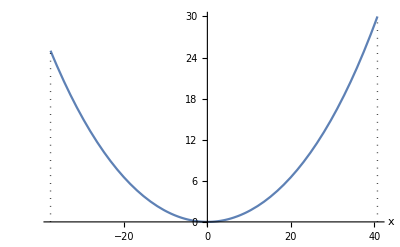

```mathematica
y==a Cosh[x/a]-a
SCMAF[%,RA,{At[2],a==31.7505},
Plot,{At[2],{x,-37.6066,40.7843},AxesLabel->Automatic,Epilog->{Dotted,Line[{{-37.6066,0},{-37.6066,25}}],Line[{{40.7843,0},{40.7843,30}}]}},Part->2]
```